## Ответ на вопрос с 1 занятия: Как увеличить качество динамически изменяемого графика?

```mathematica
Manipulate[
ContourPlot[Abs[x]^α+Abs[y]^α==1,{x,-1.1,1.1},{y,-1.1,1.1},
PerformanceGoal->"Quality"],
{α,0.2,3}]
```

```mathematica
Manipulate[
ContourPlot[Abs[x]^α+Abs[y]^α==1,{x,-1.1,1.1},{y,-1.1,1.1}],
{α,0.2,3}]
```

## Домашнее задание (решение)

Построить функцию

```mathematica
x Boole@OddQ@Floor[15x]+Sin@x
```

по x от 0 до π. На примере этой функции подумайте, зачем символу Plot нужен атрибут HoldAll.

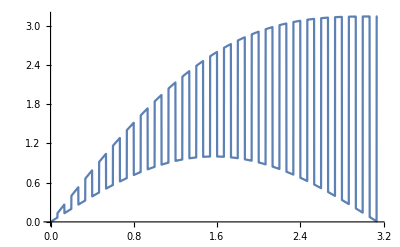

```mathematica
Plot[x Boole@OddQ@Floor[15x]+Sin@x,{x,0,π}]
```

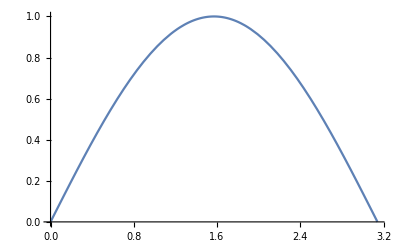

```mathematica
expr=x Boole@OddQ@Floor[15x]+Sin@x;
Plot[expr,{x,0,π}]
```

# Задание переменных и функций

## Правила замены

Ядерные правила замены символов

Упражнение. В алгоритме вычисления выражений был пункт проверки применения правил. На работу совокупности каких функций это похоже?

Ядерные правила замены символов бывают нескольких типов. В рамках этой лекции будет рассказано про два из них.

## OwnValues: значения самого символа

Такие правила применяются при вычислении символов. Например:

```mathematica
t=4;
```

```mathematica
(*OwnValues — функция, которая возвращает список правил описываемого типа для символа, переданного в него как аргумент*)
OwnValues@t
```

{HoldPattern[t]:>4}

Так как правил для символа может быть несколько, они представлены в виде списка (List, помните?).

Упражнение: понять, зачем в правиле нужна функция HoldPattern.

Если вспомнить нашу схему вычисления, то данный тип правил применяется в обведённом овалом месте:

Список правил OwnValues можно задавать напрямую (но так почти никогда не делается):

```mathematica
OwnValues[t]={HoldPattern@t:>5};
```

Упражнение. Задать собственное значение для символа x при условии, что символ y не равен нулю.

## DownValues: значения символа как функции

Этот тип правил применяется при вычислении сложного выражения, голова которого является символом, к которому и относятся эти правила. То есть данные правила работают на этом этапе алгоритма вычисления:

Пример. Для символа f задано правило DownValues следующего вида: HoldPattern[f[x_]] :> x^2
Поэтому если какое-то сложное выражение после вычисления своих головы и аргументов будет иметь голову f и один аргумент любого вида, то правило применится, и выражение заменится на квадрат единственного аргумента.

Список правил DownValues можно задавать напрямую, как и OwnValues (но так тоже не делается):

```mathematica
DownValues@f={HoldPattern[f[x_]]:>x^2}
```

{HoldPattern[f[x_]]:>x^2}

```mathematica
f[something]
```

something^2

## Unevaluated

Удержать от вычисления один из аргументов.

```mathematica
f@x_:=StringLength@ToString[x,InputForm]
f[x^2]
f[2^2]
f[Unevaluated[2^2]]
```

```mathematica
f@x_:=StringLength@ToString[Unevaluated@x,InputForm]
f[x^2]
f[2^2]
f[Unevaluated[2^2]]
```

Unevaluated снимается только во время применения правил:

```mathematica
f[x_]:=x^2
```

```mathematica
f@Unevaluated[2+2]
g@Unevaluated[2+2]
```

16

g[Unevaluated[2+2]]

*Упражнение: объяснить, почему результаты различны:

```mathematica
MatchQ[a+b,#]&/@{Unevaluated[_+_],HoldPattern[_+_]}
```

{False,True}

## Функции Set «=» и SetDelayed «:=»

OwnValues и DownValues можно сформировать не только прямым заданием, как описано в предыдущем пункте. Наиболее распространённый способ заключается в применении функций Set и SetDelayed.

Упражнение: по аналогии с Rule и RuleDelayed объяснить, в чём различие между Set и SetDelayed.

Там, где это возможно, будем сразу использовать краткие формы записи этих функций (см. заголовок данного пункта).

И OwnValues, и DownValues (и UpValues...) должны быть присобачены к конкретному символу.

```mathematica
y_[x_]:=y^x
```

SetDelayed::nosym: y_[x_] does not contain a symbol to attach a rule to.

$Failed

Правила для конкретного шаблона можно перезаписывать. Если шаблонов несколько для одного символа, то при перезаписи одного остальные останутся неизменными.

## Примеры

ClearAll очищает и OwnValues, и DownValues символа

```mathematica
ClearAll@f
```

```mathematica
f[x_]:=Sin@x/x
```

```mathematica
f[0]
```

Упражнение. Как сделать так, чтобы предел не вычислялся каждый раз при вычислении f[0]?

```mathematica
Plot
```

```mathematica
Table
```

Упражнение. Как избавиться от Indeterminate?

Упражнения.

как задать функцию так, чтобы она сохраняла однажды вычисленные значения?

Создать рекуррентную формулу вычисления чисел Фибоначчи.

Сначала без сохранения значений.

Затем оптимизировать, используя сохранение значений.

Сравнить времена выполнения (Timing) для числа 30.

Найти и применить встроенную функцию вычисления числа Фибоначчи. Сравнить время её выполнения с нашим оптимизированным вариантом для числа 1000.

*Доработать оптимизированный вариант: изменить шаблон функции так, чтобы была защита от дурака, а именно:

нельзя было запустить функцию от не натуральных чисел;

нельзя было запустить функцию от слишком больших натуральных чисел, т.е. на которых выдаётся ошибка превышения глубины рекурсии.

## Домашнее задание

Задать правила работы функции специального умножения Wedge (Esc, Shift+6, Esc) при работе с грассманновыми числами — выражениями с головой g.

Если в выражении Wedge встретятся два одинаковых грассманновых числа (например, g[1] и g[1]), то выражение тождественно нулю: g[1] ⋀ x ⋀ g[2] ⋀ g[1] = 0.

Wedge только от грассманновых чисел, стоящих не в алфавитном порядке, равен знаку перестановки, умноженному на Wedge от отсортированных чисел: g[3] ⋀ g[2] ⋀ g[1] = (-1) * g[1]⋀g[2]⋀g[3].

Если в выражении Wedge одним из “множителей” является выражение, не зависящее от грассманновых чисел, то оно выносится за Wedge как обычный множитель: g[1] ⋀ 4 ⋀ g[2] = 4 * g[1]⋀g[2]

Wedge обладает свойством дистрибутивности относительно сложения.

Умножение внутри Wedge при раскрытии скобок превращается в Wedge: g[1] ^ (c * g[3]) = g[1] ^ c ^ g[3].

Как и в обычном умножении, продумать случаи запуска Wedge от одного и нуля аргументов (поверьте, они будут).

Wedge обладает свойством ассоциативности. За это отвечает один из стандартных атрибутов. Это правило нужно запускать после всех предыдущих, иначе возникнут ошибки. Если вы сделали не так, запустите ClearAll@Wedge и запустите заново все правила выше.

Проверьте себя на следующем примере:

```mathematica
(d+g@1)⋀(g@2-g@3⋀-g@1+c-g@6⋀g@5)
```

c g[1]+g[1]⋀g[2]+d (c+g[2]-g[1]⋀g[3]+g[5]⋀g[6])+g[1]⋀g[5]⋀g[6]

Если ответ совпал, вы, вероятно, сделали всё верно.